```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0
```

Y^(0,1)[x,t]-𝒟 Y^(2,0)[x,t]==0

```mathematica
f0[t_]:=1-1/2 a t^2
```

```mathematica
f1[t_]:=1
```

```mathematica
g0[x_]:=1
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→1+1/2 a t^2 (-1+x)+(2 a (-1+ⅇ^(-π^2 t 𝒟 K[1]^2)+π^2 t 𝒟 K[1]^2) Sin[π x K[1]])/(π^5 𝒟 K[1]^5)K[1]1∞}}

```mathematica
Yf[x_,t_]:=Y[x,t]/.sol[[1]]
```

```mathematica
Yf[x_,t_,a_,𝒟_]:=1+1/2 a t^2(x-1)+∑_(k=1)^100 (2a( ⅇ^(-π^2 t 𝒟 k^2)-1+π^2 t 𝒟 k^2) Sin[π x k])/(π^5 𝒟 k^5)
```

```mathematica
aa=1;
```

```mathematica
dd=1;
```

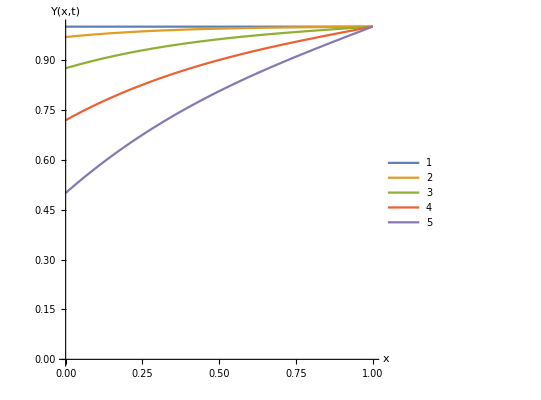

```mathematica
Plot[{Yf[x,0,aa,dd],Yf[x,0.25,aa,dd],Yf[x,0.5,aa,dd],Yf[x,0.75,aa,dd],Yf[x,1,aa,dd]},{x,0,1},PlotRange->{0,1},AxesLabel->{"x","Y(x,t)"},PlotLegends->Automatic,AspectRatio->1]
```